Progetto Quesito TC - RISAFI NATALE FRANCESCO PIO 223491

```mathematica
A=({{-5, -141, -8, 72}, {3, 71, 4, -36}, {-2, -69, -5, 35}, {4, 139, 8, -72}})
```

{{-5,-141,-8,72},{3,71,4,-36},{-2,-69,-5,35},{4,139,8,-72}}

```mathematica
MatrixForm[A]
```

(-5 | -141 | -8 | 72
3 | 71 | 4 | -36
-2 | -69 | -5 | 35
4 | 139 | 8 | -72)

```mathematica
(*Per il calcolo dei modi naturali, analizziamo gli autovalori ed il polinomio caratteristico della matrice A.*)
```

```mathematica
Eigenvalues[A]
```

{-5,-2,-2,-2}

```mathematica
Simplify[CharacteristicPolynomial[A,λ]]
```

```mathematica
(2+λ)^3 (5+λ)
```

```mathematica
(*Analizziamo adesso la matrice Ã, che rappresenta la forma canonica di Jordan, innanzitutto calcolo il numero di autovettori linearmente indipendenti che caratterizzano il sottospazio, per il calcolo della molteplicità geometrica:*)
```

```mathematica
NullSpace[A+2IdentityMatrix[4]]
```

{{-10,6,-3,11}}

```mathematica
(*Dopo aver calcolato la molteplicità geometrica, valuto la forma canonica Jordan:*)
```

```mathematica
J = JordanDecomposition[A]
```

{{{-220,-10,9/11,59/121},{120,6,-1/11,-20/121},{-99,-3,28/11,318/121},{224,11,0,0}},{{-5,0,0,0},{0,-2,1,0},{0,0,-2,1},{0,0,0,-2}}}

```mathematica
(*Ne metto in evidenza la matrice di cambiamento di base, che rappresenta il primo argomento:*)
```

```mathematica
Map[MatrixForm, J]
```

{(-220 | -10 | 9/11 | 59/121
120 | 6 | -1/11 | -20/121
-99 | -3 | 28/11 | 318/121
224 | 11 | 0 | 0),(-5 | 0 | 0 | 0
0 | -2 | 1 | 0
0 | 0 | -2 | 1
0 | 0 | 0 | -2)}

```mathematica
Ã = JordanDecomposition [A][[2]]
```

{{-5,0,0,0},{0,-2,1,0},{0,0,-2,1},{0,0,0,-2}}

```mathematica
Ã
```

{{-5,0,0,0},{0,-2,1,0},{0,0,-2,1},{0,0,0,-2}}

```mathematica
MatrixForm[Ã]
```

(-5 | 0 | 0 | 0
0 | -2 | 1 | 0
0 | 0 | -2 | 1
0 | 0 | 0 | -2)

```mathematica
(*Analizzo adesso l'esponenziale di matrice, per evidenziare i modi naturali del sistema:*)
```

```mathematica
MatrixExp[Ã t]
```

{{ⅇ^(-5 t),0,0,0},{0,ⅇ^(-2 t),ⅇ^(-2 t) t,1/2 ⅇ^(-2 t) t^2},{0,0,ⅇ^(-2 t),ⅇ^(-2 t) t},{0,0,0,ⅇ^(-2 t)}}

```mathematica
MatrixForm[MatrixExp[Ã t]]
```

(ⅇ^(-5 t) | 0 | 0 | 0
0 | ⅇ^(-2 t) | ⅇ^(-2 t) t | 1/2 ⅇ^(-2 t) t^2
0 | 0 | ⅇ^(-2 t) | ⅇ^(-2 t) t
0 | 0 | 0 | ⅇ^(-2 t))

```mathematica
(*Ipotizzando lo stato iniziale:*)
```

```mathematica
Subscript[x, 0]= ({{1}, {0}, {0}, {0}})
```

{{1},{0},{0},{0}}

```mathematica
(*Passo adesso al calcolo della risposta libera:*)
```

```mathematica
Subscript[x, l][t_]:=Expand[Simplify[ MatrixExp[A t].Subscript[x, 0]]]
```

```mathematica
Subscript[x, l][t]
```

{{-440/27 ⅇ^(-5 t)+(467 ⅇ^(-2 t))/27-467/9 ⅇ^(-2 t) t+55/3 ⅇ^(-2 t) t^2},{(80 ⅇ^(-5 t))/9-(80 ⅇ^(-2 t))/9+89/3 ⅇ^(-2 t) t-11 ⅇ^(-2 t) t^2},{-22/3 ⅇ^(-5 t)+(22 ⅇ^(-2 t))/3-24 ⅇ^(-2 t) t+11/2 ⅇ^(-2 t) t^2},{(448 ⅇ^(-5 t))/27-(448 ⅇ^(-2 t))/27+484/9 ⅇ^(-2 t) t-121/6 ⅇ^(-2 t) t^2}}

```mathematica
MatrixForm[Subscript[x, l][t]]
```

(-440/27 ⅇ^(-5 t)+(467 ⅇ^(-2 t))/27-467/9 ⅇ^(-2 t) t+55/3 ⅇ^(-2 t) t^2
(80 ⅇ^(-5 t))/9-(80 ⅇ^(-2 t))/9+89/3 ⅇ^(-2 t) t-11 ⅇ^(-2 t) t^2
-22/3 ⅇ^(-5 t)+(22 ⅇ^(-2 t))/3-24 ⅇ^(-2 t) t+11/2 ⅇ^(-2 t) t^2
(448 ⅇ^(-5 t))/27-(448 ⅇ^(-2 t))/27+484/9 ⅇ^(-2 t) t-121/6 ⅇ^(-2 t) t^2)

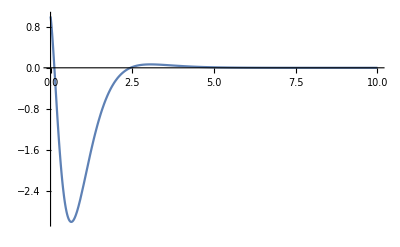

```mathematica
Plot[Subscript[x, l][t][[1]], {t,0,10},PlotRange-> Full]
```

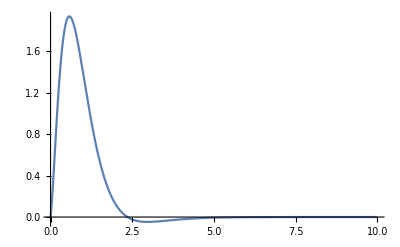

```mathematica
Plot[Subscript[x, l][t][[2]], {t,0,10},PlotRange-> Full]
```

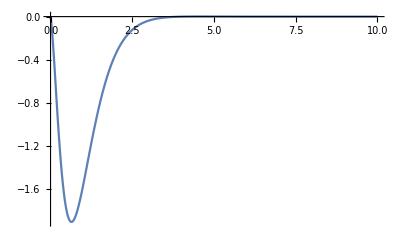

```mathematica
Plot[Subscript[x, l][t][[3]], {t,0,10},PlotRange-> Full]
```

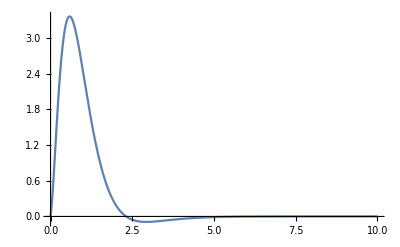

```mathematica
Plot[Subscript[x, l][t][[4]], {t,0,10},PlotRange-> Full]
```

```mathematica
(*Per studiare i vari stati iniziali in maniera tale da attivare, e non attivare, qualche modo naturale nella risposta libera, riprendo la matrice di cambiamento di base e la forma canonica di Jordan. *)
```

```mathematica
T = JordanDecomposition[A][[1]]
```

{{-220,-10,9/11,59/121},{120,6,-1/11,-20/121},{-99,-3,28/11,318/121},{224,11,0,0}}

```mathematica
MatrixForm[T]
```

(-220 | -10 | 9/11 | 59/121
120 | 6 | -1/11 | -20/121
-99 | -3 | 28/11 | 318/121
224 | 11 | 0 | 0)

```mathematica
MatrixForm[JordanDecomposition[A][[2]]]
```

(-5 | 0 | 0 | 0
0 | -2 | 1 | 0
0 | 0 | -2 | 1
0 | 0 | 0 | -2)

```mathematica
(*Assegnando vari vettori "allineati" con le colonne della matrice di cambiamento di base che attiveranno la rispettiva colonna nella nostra matrice canonica, che contiene i modi naturali corrispondenti:*)
```

```mathematica
Subscript[x, 0] = ({{-220}, {120}, {-99}, {224}})
```

{{-220},{120},{-99},{224}}

```mathematica
Subscript[x, l][t_]:=Expand[Simplify[ MatrixExp[A t].Subscript[x, 0]]]
```

```mathematica
Subscript[x, l][t]
```

{{-220 ⅇ^(-5 t)},{120 ⅇ^(-5 t)},{-99 ⅇ^(-5 t)},{224 ⅇ^(-5 t)}}

```mathematica
MatrixForm[Subscript[x, l][t]]
```

```mathematica
Subscript[x, l][t]=({{-220 ⅇ^(-5 t)}, {120 ⅇ^(-5 t)}, {-99 ⅇ^(-5 t)}, {224 ⅇ^(-5 t)}})
```

```mathematica
(*Invece volendo azzerare nella risposta libera solo la presenza dei modi polinomial-esponenziali, devo scegliere una combinazione lineare di stato iniziale tra due vettori "allineati" con le rispettive colonne della matrice T (prima e seconda colonna).*)
```

```mathematica
Subscript[x, 0] = ({{-220}, {120}, {-99}, {224}})+({{-10}, {6}, {-3}, {11}})
```

{{-230},{126},{-102},{235}}

```mathematica
Subscript[x, l][t_]:=Expand[Simplify[ MatrixExp[A t].Subscript[x, 0]]]
```

```mathematica
Subscript[x, l][t]
```

{{-220 ⅇ^(-5 t)-10 ⅇ^(-2 t)},{120 ⅇ^(-5 t)+6 ⅇ^(-2 t)},{-99 ⅇ^(-5 t)-3 ⅇ^(-2 t)},{224 ⅇ^(-5 t)+11 ⅇ^(-2 t)}}

```mathematica
MatrixForm[Subscript[x, l][t]]
```

(-220 ⅇ^(-5 t)-10 ⅇ^(-2 t)
120 ⅇ^(-5 t)+6 ⅇ^(-2 t)
-99 ⅇ^(-5 t)-3 ⅇ^(-2 t)
224 ⅇ^(-5 t)+11 ⅇ^(-2 t))

```mathematica
Subscript[x, 0] = ({{59/121}, {-20/121}, {318/121}, {0}})
```

{{59/121},{-20/121},{318/121},{0}}

```mathematica
Subscript[x, l][t_]:=Expand[Simplify[ MatrixExp[A t].Subscript[x, 0]]]
```

```mathematica
MatrixForm[Subscript[x, l][t]]
```

((59 ⅇ^(-2 t))/121+9/11 ⅇ^(-2 t) t-5 ⅇ^(-2 t) t^2
-20/121 ⅇ^(-2 t)-1/11 ⅇ^(-2 t) t+3 ⅇ^(-2 t) t^2
(318 ⅇ^(-2 t))/121+28/11 ⅇ^(-2 t) t-3/2 ⅇ^(-2 t) t^2
11/2 ⅇ^(-2 t) t^2)

```mathematica
Subscript[x, 0] = 2({{-10}, {6}, {-3}, {11}})
```

{{-20},{12},{-6},{22}}

```mathematica
Subscript[x, l][t_]:=Expand[Simplify[ MatrixExp[A t].Subscript[x, 0]]]
```

```mathematica
MatrixForm[Subscript[x, l][t]]
```

```mathematica
Subscript[x, l][t]=({{-20 ⅇ^(-2 t)}, {12 ⅇ^(-2 t)}, {-6 ⅇ^(-2 t)}, {22 ⅇ^(-2 t)}})
```

```mathematica
(*Analizzo la funzione di trasferimento del sistema dinamico (F.D.T.), essa sarà un rapporto tra due polinomi, essendo il sistema scalare, che dipenderà dai parametri del sistema, cioè le matirci A,B,C,D, se presente.*)
```

```mathematica
A=({{-5, -141, -8, 72}, {3, 71, 4, -36}, {-2, -69, -5, 35}, {4, 139, 8, -72}})
```

{{-5,-141,-8,72},{3,71,4,-36},{-2,-69,-5,35},{4,139,8,-72}}

```mathematica
B = ({{-2}, {1}, {-1}, {2}})
```

{{-2},{1},{-1},{2}}

```mathematica
Dd = 0
```

0

```mathematica
Cc = ({{1, -1, 1, 2}})
```

{{1,-1,1,2}}

```mathematica
G[s_] := Simplify[Cc.Inverse[s IdentityMatrix[4]-A].B+Dd]
```

```mathematica
G[s]
```

{{(1+2 s)/((2+s)^3 (5+s))}}

```mathematica
G[s][[1]]
```

{(1+2 s)/((2+s)^3 (5+s))}

```mathematica
(*Calcolo dei poli del sistema, valori che azzerano il denominatore della funzione di trasferimento, che in questo caso corrispondono con gli autovalori del sistema, il numero di stati del sistema è pari al grado massimo del denominatore:*)
```

```mathematica
Solve[Denominator[G[s]]==0,s]
```

{{s→-5},{s→-2},{s→-2},{s→-2}}

```mathematica
(* Calcolo degli zeri del sistema, valori che azzerano il numeratore della funzione di trasferimento:*)
```

```mathematica
Solve[Numerator[G[s]]==0,s]
```

{{s→-1/2}}

```mathematica
(*Passo al calcolo della risposta all'impulso, definita come l'antitrasformata di Laplace della funzione di trasferimento.*)
```

```mathematica
G[s][[1,1]]
```

(1+2 s)/((2+s)^3 (5+s))

```mathematica
(*Analizzando i poli della F.D.T. che coincidono con gli autovalori della matrice A:*)
```

```mathematica
Solve[Denominator[G[s]] == 0, s]
```

{{s→-5},{s→-2},{s→-2},{s→-2}}

```mathematica
(*I abbiamo 4 poli per questo sistema ed ognuno di essi genera un modo naturale; riscrivo l'espansione in fratti semplici della F.D.T., usando la funzione "apart":*)
```

```mathematica
Apart[G[s]][[1,1]]
```

-1/(2+s)^3+1/(2+s)^2-1/(3 (2+s))+1/(3 (5+s))

```mathematica
(*Adesso calcolo i vari coefficienti tramite la formula di Heaviside per ottenere la risposta all'impulso: Subscript[C, 23] 1/(2+s)^3+Subscript[C, 22] 1/(2+s)^2+Subscript[C, 21] 1/(2+s)+Subscript[C, 1] 1/(5+s)*)
```

```mathematica
Subscript[C, 1]= lim_(s->-5) (s+5)G[s][[1,1]]
```

1/3

```mathematica
Subscript[C, 23]= lim_(s->-2) (s+2)^3 G[s][[1,1]]
```

-1

```mathematica
Subscript[C, 22]= 1/(1!)lim_(s->-2) D[((s+2)^3 G[s])[[1,1]], s]
```

1

```mathematica
Subscript[C, 21]= 1/(2!)lim_(s->-2) D[(D[(((s+2))^3 G[s]), s])[[1,1]], s]
```

-1/3

```mathematica
(*Dopo aver calcolato i vari coefficienti, effettuato le antitrasformate di Laplace per ogni termine moltiplicato da un coefficiente, per riportare tutto nel dominio del tempo, possiamo verificare grazie a Mathematica la correttezza della risposta all'impulso:*)
```

```mathematica
g[t_]:=Expand[InverseLaplaceTransform[G[s],s,t]]
```

```mathematica
g[t][[1,1]]
```

ⅇ^(-5 t)/3-ⅇ^(-2 t)/3+ⅇ^(-2 t) t-1/2 ⅇ^(-2 t) t^2

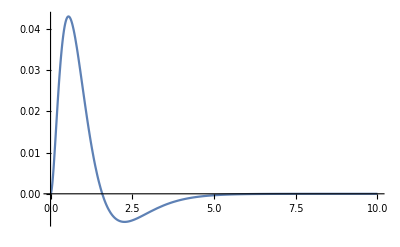

```mathematica
Plot[g[t],{t,0,10}, PlotRange->Full]
```

```mathematica
(*Essendo rispettate le condizioni del teorema del valore finale per la L-trasformata, continuità ed esistenza di questo limite:*)
```

```mathematica
lim_(t->+∞) g[t]
```

{{0}}

```mathematica
(*Possiamo dimostrare la convergenza a zero della nostra risposta all'impulso, tramite il teorema del valore finale per la L-trasformata:*)
```

```mathematica
lim_(s->0) s G[s]
```

{{0}}

```mathematica
(*Calcolo della risposta al gradino; scrivo la relazioe che lega la risposta al gradino alla funzione di trasferimento.*)
```

```mathematica
u[s_] = Expand[LaplaceTransform[1,t,s]]
```

1/s

```mathematica
Subscript[Y, f][s_]:= G[s][[1,1]]u[s]
```

```mathematica
Subscript[Y, f][s]
```

(1+2 s)/(s (2+s)^3 (5+s))

```mathematica
(*Adesso riscrivo in fratti semplici la Subscript[Y, f][s]*)
```

```mathematica
Apart[Subscript[Y, f][s]]
```

1/(40 s)+1/(2 (2+s)^3)-1/(4 (2+s)^2)+1/(24 (2+s))-1/(15 (5+s))

```mathematica
(*Riscrivendo in maniera simbolica i fratti semplici, applico la formula generalizzata di Heaviside per calcolare i coefficienti Subscript[C, ij]:
Subscript[C, 1]/s+Subscript[C, 23]/(2+s)^3+Subscript[C, 22]/(2+s)^2+Subscript[C, 21]/(2+s)+Subscript[C, 3]/(5+s)*)
```

```mathematica
Subscript[C, 1]= lim_(s->0) s Subscript[Y, f][s]
```

1/40

```mathematica
Subscript[C, 3]=lim_(s->-5) (s+5)Subscript[Y, f][s]
```

-1/15

```mathematica
Subscript[C, 23]= lim_(s->-2) (s+2)^3 Subscript[Y, f][s]
```

1/2

```mathematica
Subscript[C, 22]= 1/(1!)lim_(s->-2) D[((s+2)^3 Subscript[Y, f][s]), s]
```

-1/4

```mathematica
Subscript[C, 21]= 1/(2!)lim_(s->-2) D[(D[(((s+2))^3 Subscript[Y, f][s]), s]), s]
```

1/24

```mathematica
(*Una volta calcolati tutti i coefficienti  Subscript[C, ij], possiamo applicare le antitrasformate di Laplace per formare la risposta al gradino unitario:
L^-1 1/s := 1(t)    (La trasformata di Laplace del gradino è 1/s)
L^-1 1/(2+s)^3 := t^2/2 e^(-2t) 1(t)
L^-1 1/(2+s)^2:= te^(-2t) 1(t)
L^-1 1/(2+s):= e^(-2t) 1(t)
L^-1 1/(5+s):= e^(-5t) 1(t)*)
```

```mathematica
Subscript[y, f][t_]:= Expand[InverseLaplaceTransform[Subscript[Y, f][s],s,t]]
```

```mathematica
Subscript[y, f][t]
```

1/40-ⅇ^(-5 t)/15+ⅇ^(-2 t)/24-1/4 ⅇ^(-2 t) t+1/4 ⅇ^(-2 t) t^2

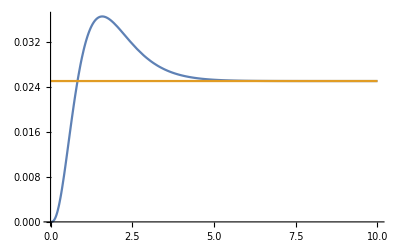

```mathematica
Plot[{Subscript[y, f][t],1/40},{t,0,10}, PlotRange->Full]
```

```mathematica
(*Per calcolare la risposta forzata al segnale periodico  u(t) = sin(t) 1(t), ripeto il ragionamento precedente considerando come ingresso il segnale periodico elementare u(t) = sin(t) 1(t);*)
```

```mathematica
U[t_] := Sin[t]
```

```mathematica
u[s_]:=Expand[LaplaceTransform[U[t],t,s]]
```

```mathematica
u[s]
```

1/(1+s^2)

```mathematica
Subscript[Y, f1][s_]:= G[s][[1,1]]u[s]
```

```mathematica
Subscript[Y, f1][s]
```

(1+2 s)/((2+s)^3 (5+s) (1+s^2))

```mathematica
(*Eseguiamo l'espansione in fratti semplici:*)
```

```mathematica
Apart[Subscript[Y, f1][s]]
```

-1/(5 (2+s)^3)+1/(25 (2+s)^2)+2/(375 (2+s))+1/(78 (5+s))+(113-59 s)/(3250 (1+s^2))

```mathematica
(*Mathematica non scompone il denominatore con componenti complesse e coniugate (s^2+1), che possiamo scomporre in (s-ⅈ)(s+ⅈ). Dunque la nostra espansione in fratti semplici sarà:
Subscript[D, 23]/(2+s)^3+Subscript[D, 22]/(2+s)^2+Subscript[D, 21]/(2+s)+Subscript[D, 1]/(5+s)+Subscript[D, 3]/(s+i)+Subscript[-_D, 3]/(s-i) . Posso adesso calcolare i coefficienti Subscript[D, ij] con le formule di Heaviside.*)
```

```mathematica
Subscript[D, 1] = lim_(s->-5) (5+s)Subscript[Y, f1][s]
```

1/78

```mathematica
Subscript[D, 23] = lim_(s->-2) (2+s)^3 Subscript[Y, f1][s]
```

-1/5

```mathematica
Subscript[D, 22] = lim_(s->-2) D[((2+s)^3 Subscript[Y, f1][s]), s]
```

1/25

```mathematica
Subscript[D, 21] = 1/(2!)  lim_(s->-2) D[(D[((2+s)^3 Subscript[Y, f1][s]), s]), s]
```

2/375

```mathematica
Subscript[D, 3]= lim_(s->-ⅈ) (s+ⅈ)Subscript[Y, f1][s]
```

-59/6500+(113 ⅈ)/6500

```mathematica
(*OverBar[Subscript[D, 3]] non è nient'altro che il valore complesso e coniugato di Subscript[D, 3].
Dunque la risposta in s sarà pari a:
-1/5 1/(2+s)^3+1/25 1/(2+s)^2+2/375 1/(2+s)+1/78 1/(5+s)+((-59/6500+(113ⅈ)/6500)1/(s+i))+((-59/6500-(113ⅈ)/6500)1/(s-i))
Riscrivendo in maniera ordinata:
((-59/6500+(113ⅈ)/6500)1/(s+i))+((-59/6500-(113ⅈ)/6500)1/(s-i))- 1/5 1/(2+s)^3+1/25 1/(2+s)^2+2/375 1/(2+s)+1/78 1/(5+s)
Passando al dominio in t:
((-59/6500+(113ⅈ)/6500)e^-ⅈt)+((-59/6500-(113ⅈ)/6500)e^ⅈt)-1/5 t^2/2 e^(-2t)1(t)+1/25 te^(-2t) 1(t)+2/375 e^(-2t)1(t)+1/78 e^(-5t)1(t)
La risposta a regime, il primo addendo, la si può riscrivere come:
((-59/6500+(113ⅈ)/6500)e^-ⅈt)+((-59/6500-(113ⅈ)/6500)e^ⅈt) = 2 Re[ (-59/6500-(113ⅈ)/6500)e^ⅈt] = 2 Re[(-59/6500-(113ⅈ)/6500)(Cos[t]+ⅈSin[t])]
Per ottenere il risultato sfrutto mathematica: *)
```

```mathematica
ComplexExpand[Subscript[D, 3] ⅇ^(- ⅈ t)+Conjugate[Subscript[D, 3]] ⅇ^(ⅈ t)]
```

-(59 Cos[t])/3250+(113 Sin[t])/3250

```mathematica
(* Verificando con Methematica, attraverso l'anti-trasformata di Laplace della nostra risposta al segnale periodico nel dominio s, la validità della risposta all'ingresso periodico sin(t), noto che le due espressioni combaciano: *)
```

```mathematica
Subscript[y, f][t_]:= Expand[InverseLaplaceTransform[Subscript[Y, f1][s],s,t]]
```

```mathematica
Subscript[y, f][t]
```

ⅇ^(-5 t)/78+(2 ⅇ^(-2 t))/375+1/25 ⅇ^(-2 t) t-1/10 ⅇ^(-2 t) t^2-(59 Cos[t])/3250+(113 Sin[t])/3250

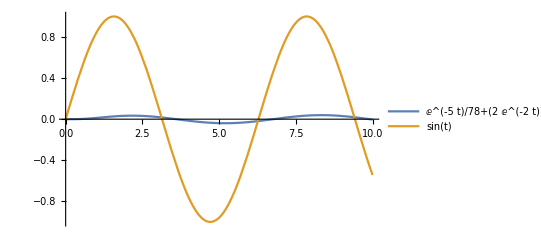

```mathematica
Plot[{ⅇ^(-5 t)/78+(2 ⅇ^(-2 t))/375+1/25 ⅇ^(-2 t) t-1/10 ⅇ^(-2 t) t^2-(59 Cos[t])/3250+(113 Sin[t])/3250,Sin[t]},{t,0,10},PlotLegends->"Expressions"]
```

```mathematica
(* Tra il nostro ingresso e la risposta forzata calcolata rispetto l'ingresso, noto che cambia l'ampiezza e dunque lo sfasamento che posso calcolare: *)
```

```mathematica
Solve[{Y Sin[θ]==-59/3250,Y Cos[θ]==113/3250,Y>0},{Y,θ}]
```

{{Y→ConditionalExpression[1/(5 √26), C[1]∈ℤ],θ→ConditionalExpression[2 ArcTan[(-650+113 √26)/(59 √26)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
(* Calcolo di un modello I/U per rappresentare il sistema dinamico, da un'identità algebrica passo ad un'identità differenziale nel dominio del tempo (2+s)^3(5+s)Subscript[y, f](s)=U(s)(1+2s)
s^4 Subscript[y, f](s)+11 s^3 Subscript[y, f](s)+42 s^2 Subscript[y, f](s)+68sSubscript[y, f](s)+40Subscript[y, f](s)=2sU(s)+U(s)
Passando nel dominio del tempo, tramite il teorema della derivata di ordine n per la trasformata di Laplace:
Subscript[y^(4), f](t)+11Subscript[y^(3), f](t)+42Subscript[y', f](t)+68 Subscript[y', f](t)+40Subscript[y, f](t)=2 U'(t)+U(t) *)
```

```mathematica
Eqdiff = Y''''[t]+11Y'''[t]+42Y''[t]+68Y'[t]+40Y[t]==2 u'[t]+u[t]
```

40 Y[t]+68 Y'[t]+42 Y''[t]+11 Y^(3)[t]+Y^(4)[t]==u[t]+2 u'[t]

```mathematica
(*Trasformo l'equazione differenziale in equazione nel dominio s: *)
```

```mathematica
LaplaceTransform[Eqdiff,t,s]
```

40 LaplaceTransform[Y[t],t,s]+s^4 LaplaceTransform[Y[t],t,s]+68 (s LaplaceTransform[Y[t],t,s]-Y[0])-s^3 Y[0]+42 (s^2 LaplaceTransform[Y[t],t,s]-s Y[0]-Y'[0])-s^2 Y'[0]+11 (s^3 LaplaceTransform[Y[t],t,s]-s^2 Y[0]-s Y'[0]-Y''[0])-s Y''[0]-Y^(3)[0]==LaplaceTransform[u[t],t,s]+2 (s LaplaceTransform[u[t],t,s]-u[0])

```mathematica
(*Sostituisco i simboli Y(s) ed U(s) *)
```

```mathematica
%/.{LaplaceTransform[Y[t],t,s]->Y[s],LaplaceTransform[u[t],t,s]->U[s]}
```

-s^3 Y[0]+40 Y[s]+s^4 Y[s]+68 (-Y[0]+s Y[s])+42 (-s Y[0]+s^2 Y[s]-Y'[0])-s^2 Y'[0]+11 (-s^2 Y[0]+s^3 Y[s]-s Y'[0]-Y''[0])-s Y''[0]-Y^(3)[0]==U[s]+2 (-u[0]+s U[s])

```mathematica
(*Azzero la quantità U[0]: *)
```

```mathematica
Eqdiffs=%/.{u[0]->0}
```

-s^3 Y[0]+40 Y[s]+s^4 Y[s]+68 (-Y[0]+s Y[s])+42 (-s Y[0]+s^2 Y[s]-Y'[0])-s^2 Y'[0]+11 (-s^2 Y[0]+s^3 Y[s]-s Y'[0]-Y''[0])-s Y''[0]-Y^(3)[0]==U[s]+2 s U[s]

```mathematica
(* Risolvo l'equazione nel dominio s, secondo Y[s] *)
```

```mathematica
Solve[Eqdiffs,Y[s]]
```

{{Y[s]→(U[s]+2 s U[s]+68 Y[0]+42 s Y[0]+11 s^2 Y[0]+s^3 Y[0]+42 Y'[0]+11 s Y'[0]+s^2 Y'[0]+11 Y''[0]+s Y''[0]+Y^(3)[0])/((2+s)^3 (5+s))}}

```mathematica
(* Separo la componente forzata dalla risposta libera: *)
```

```mathematica
Rispostas=Solve[Eqdiffs,Y[s]][[1,1]][[2]]
```

(U[s]+2 s U[s]+68 Y[0]+42 s Y[0]+11 s^2 Y[0]+s^3 Y[0]+42 Y'[0]+11 s Y'[0]+s^2 Y'[0]+11 Y''[0]+s Y''[0]+Y^(3)[0])/((2+s)^3 (5+s))

```mathematica
Collect[Rispostas,U[s]]
```

((1+2 s) U[s])/((2+s)^3 (5+s))+(68 Y[0]+42 s Y[0]+11 s^2 Y[0]+s^3 Y[0]+42 Y'[0]+11 s Y'[0]+s^2 Y'[0]+11 Y''[0]+s Y''[0]+Y^(3)[0])/((2+s)^3 (5+s))

```mathematica
(* La risposta libera sarà la seconda componente: *)
```

```mathematica
Risplibera=%[[2]]
```

(68 Y[0]+42 s Y[0]+11 s^2 Y[0]+s^3 Y[0]+42 Y'[0]+11 s Y'[0]+s^2 Y'[0]+11 Y''[0]+s Y''[0]+Y^(3)[0])/((2+s)^3 (5+s))

```mathematica
(* Per risolvere dovrò sicuramente assegnare le condizioni iniziali a partire dallo stato iniziale Subscript[x, 0]: *)
```

```mathematica
Subscript[x, 0]=({{1}, {0}, {0}, {0}})
```

{{1},{0},{0},{0}}

```mathematica
A=({{-5, -141, -8, 72}, {3, 71, 4, -36}, {-2, -69, -5, 35}, {4, 139, 8, -72}})
```

{{-5,-141,-8,72},{3,71,4,-36},{-2,-69,-5,35},{4,139,8,-72}}

```mathematica
Cc = ({{1, -1, 1, 2}})
```

{{1,-1,1,2}}

```mathematica
Y[0] = (Cc.Subscript[x, 0])[[1,1]]
```

1

```mathematica
Y'[0] = (Cc.A.Subscript[x, 0])[[1,1]]
```

-2

```mathematica
Y''[0] = (Cc.A.A.Subscript[x, 0])[[1,1]]
```

-1

```mathematica
Y'''[0] = (Cc.A.A.A.Subscript[x, 0])[[1,1]]
```

4

```mathematica
Risplibera
```

(-23+19 s+9 s^2+s^3)/((2+s)^3 (5+s))

```mathematica
(*Posso adesso calcolare la risposta libera nel dominio del tempo, usando la funzione di mathematica:*)
```

```mathematica
Expand[InverseLaplaceTransform[Risplibera,s,t]]
```

(2 ⅇ^(-5 t))/3+ⅇ^(-2 t)/3+2 ⅇ^(-2 t) t-11/2 ⅇ^(-2 t) t^2

```mathematica
(*Determino uno stato iniziale, tale che la risposta al gradino complessiva coincida con il suo valore di regime; prendo la funzione di trasferimento:*)
```

```mathematica
G[s_]:=FullSimplify[Cc.Inverse[s IdentityMatrix[4]-A].B][[1,1]]
```

```mathematica
G[s]
```

(1+2 s)/((2+s)^3 (5+s))

```mathematica
(*La sua risposta al gradino sarà Subscript[Y, f](s) = G(s) u(s), dove u(s) è la trasformata di Laplace dell'ingresso, in questo caso il gradino:*)
```

```mathematica
Subscript[Y, f][s_] = G[s]/s
```

(1+2 s)/(s (2+s)^3 (5+s))

```mathematica
(*Questa risposta sappiamo che può essere riscritta come la somma algebrica di due componenti, la risposta transitoria e la risposta a regime:
Subscript[Y, f](s) = Subscript[Y, tr](s) + Subscript[Y, ss](s) 
Determino una nuova quantità G[0], denominata guadagno statico: lim_(s->0) sSubscript[Y, f](s) = G[0]
Nel caso di risposta al gradino unitario, la risposta a regime è:
Subscript[Y, ss](s)=G[0]/s, dunque la risposta transitoria:
Subscript[Y, tr](s) = Subscript[Y, f](s) - G[0]/s *)
```

```mathematica
Subscript[Y, tr]=Simplify[Subscript[Y, f][s]-G[0]/s]
```

(-1+(40 (1+2 s))/((2+s)^3 (5+s)))/(40 s)

```mathematica
G[0]/s
```

1/(40 s)

```mathematica
(*La risposta complessiva al gradino è data dalla somma algebrica della risposta libera e della risposta forzata, dunque lo stato iniziale Subscript[x, 0], dovrà essere scelto in maniera tale che la risposta complessiva sia pari solo alla risposta a regime: Y(s) = G[0]/s   
Y(s) = Subscript[Y, l](s)+Subscript[Y, f](s)= Subscript[Y, l](s)  + Subscript[Y, tr](s) + Subscript[Y, ss](s) = (C(sI-A))^-1 Subscript[x, 0]+ Subscript[Y, tr](s)+G[0]/s
 C(sI-A)^-1 Subscript[x, 0]+ Subscript[Y, tr](s)= 0 , questa condizione dovrà essere rispettata, dovrò dunque trovare uno stato iniziale Subscript[x, 0] in grado di azzerare e compensare completamente la componente transitoria.
 Esplicitiamo l'incognita (il vettore) nella formula del calcolo della risposta libera:*)
```

```mathematica
Subscript[Y, l]=FullSimplify[Cc.Inverse[s IdentityMatrix[4]-A].({{Subscript[x, 10]}, {Subscript[x, 20]}, {Subscript[x, 30]}, {Subscript[x, 40]}})][[1,1]]
```

((-23+s (19+s (9+s))) x_10-(65+s (76+s (14+s))) x_20+(44+s (32+s (10+s))) x_30+(1+2 s) (32+s (10+s)) x_40)/((2+s)^3 (5+s))

```mathematica
(*Estraggo adesso il numeratore della riposta libera ed i suoi coefficienti:*)
```

```mathematica
numeratore=Numerator[FullSimplify[Subscript[Y, l]+Subscript[Y, tr]]]
```

40+80 s-(2+s)^3 (5+s)+40 s ((-23+s (19+s (9+s))) x_10-(65+s (76+s (14+s))) x_20+(44+s (32+s (10+s))) x_30+(1+2 s) (32+s (10+s)) x_40)

```mathematica
CoefficientList[numeratore,s]
```

{0,12-920 x_10-2600 x_20+1760 x_30+1280 x_40,-42+760 x_10-3040 x_20+1280 x_30+2960 x_40,-11+360 x_10-560 x_20+400 x_30+840 x_40,-1+40 x_10-40 x_20+40 x_30+80 x_40}

```mathematica
(*La lista dei coefficienti che comporranno il vettore è a 5 componenti (volendo contare anche la componente pari solo a zero), dunque dovranno essere tutte uguali a 0:*)
```

```mathematica
vettore=Solve[CoefficientList[numeratore,s]=={0,0,0,0,0},{Subscript[x, 10],Subscript[x, 20],Subscript[x, 30],Subscript[x, 40]}]
```

{{x_10→0,x_20→0,x_30→-1/40,x_40→1/40}}

```mathematica
(*Otterrò il vettore dello stato iniziale:*)
```

```mathematica
Subscript[x, 0]=({{vettore[[1,1]][[2]]}, {vettore[[1,2]][[2]]}, {vettore[[1,3]][[2]]}, {vettore[[1,4]][[2]]}})
```

{{0},{0},{-1/40},{1/40}}

```mathematica
(*Volendo verificare la risposta complessiva al gradino, tenendo conto di questo stato iniziale:*)
```

```mathematica
FullSimplify[FullSimplify[Cc.Inverse[s IdentityMatrix[4]-A].Subscript[x, 0]][[1,1]]+G[s]/s]
```

1/(40 s)

```mathematica
(*Quindi, ho verificato che la risposta complessiva al gradino è proprio pari alla sua risposta a regime. La cui antitrasformata di Laplace: 1/40 1(t)*)
```